```mathematica
Needs["NeffConstraint`"]
```

### Analytic preliminaries

#### LIPS out of COM

```mathematica
Clear[M2]
dΠLIPS=dΩ/(16 π^2) kD/Ei /.Ei ->p + mD
dΠi = (nD g)/(mD p)     (dp  p^2)/(8 π^2)1/(E^(β p)+1)
Integrand = Simplify[Simplify[dΠLIPS dΠi M2 Et]]
```

(dΩ kD)/(16 (mD+p) π^2)

(dp g nD p)/(8 (1+ⅇ^(p β)) mD π^2)

(d^2 dp dΩ g kD M2 nD p^3)/(64 (1+ⅇ^(p β)) (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

Mandelstam variables

```mathematica
s = Simplify[(mD + p)^2 - p^2]
t = Simplify[(Et)^2 - q^2]
u = FullSimplify[(Ef - mD)^2-Ef^2]
```

mD (mD+2 p)

-(4 d^2 mD^2 p^2)/(mD^2+2 mD p-(-1+d^2) p^2)

(mD (mD^3+3 (-1+d^2) mD p^2+2 (-1+d^2) p^3))/((mD+p-d p) (mD+p+d p))

```mathematica
Et
```

(2 d^2 mD p^2)/(-d^2 p^2+(mD+p)^2)

```mathematica
M2lD =FullSimplify[(8 e^2 eD^2 ϵ^2)/t^2((s/2)^2+(u/2)^2)] (*lepton dark matter scattering*)
```

1/(4 d^4 mD^2 p^4)e^2 eD^2 (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2

```mathematica
Integrand/.M2->M2lD
```

(dp dΩ e^2 eD^2 g kD nD (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2)/(256 d^2 (1+ⅇ^(p β)) mD^2 p (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

```mathematica
Integrate[Integrand,d]
```

(dp dΩ g kD M2 nD (-2 d p-(mD+p) Log[-mD+(-1+d) p]+(mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) (mD+p) π^4)

```mathematica
Simplify[2 π/dΩ Integrate[Integrand/.M2->M2lD,d]]
FullSimplify[((%/.d->1)-(%/.d->-1))/mD^2]
```

(dp e^2 eD^2 g kD nD ϵ^2 (-((mD+p)^2 (mD^2+4 p^2))/d-d p^2 (5 mD^2+8 mD p+4 p^2)-4 mD^2 p (mD+p) Log[mD+p-d p]+4 mD^2 p (mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) mD^2 p (mD+p) π^3)

-((dp e^2 eD^2 g kD nD ϵ^2 (mD^4+2 mD^3 p+10 mD^2 p^2+16 mD p^3+8 p^4+4 mD^2 p (mD+p) (Log[mD]-Log[mD+2 p])))/(64 (1+ⅇ^(p β)) mD^4 p (mD+p) π^3))

#### Massive case - in momentum variables

compute q and compare to massless case

```mathematica
Clear[θsol,d]
θsol = Solve[mD + √(p^2+m^2) == √(mD^2 + kD^2) + √(p^2 - 2 p d kD + kD^2 + m^2),d][[1]]
d= Simplify[d/.θsol]
PowerExpand[Series[d,{kD,0,1}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{d→(-mD^2+mD √(kD^2+mD^2)-mD √(m^2+p^2)+√(kD^2+mD^2) √(m^2+p^2))/(kD p)}

((-mD+√(kD^2+mD^2)) (mD+√(m^2+p^2)))/(kD p)

((mD+√(m^2+p^2)) kD)/(2 mD p)+O[kD]^2

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

Compute E transfered

```mathematica
(*Ef = FullSimplify[√(p^2 - 2 kD d p +kD^2+m^2)/.θsol]*)
Ef = FullSimplify[mD +√(p^2+m^2) - √(mD^2 + kD^2)]
Et =FullSimplify[√(mD^2 + kD^2)-mD]
ESM = √(p^2+m^2)
Ei = ESM + mD
```

mD-√(kD^2+mD^2)+√(m^2+p^2)

-mD+√(kD^2+mD^2)

√(m^2+p^2)

mD+√(m^2+p^2)

```mathematica
Simplify[Expand[(ESMt + mD)^2/(ESMt^2-m^2) -1]]
```

(m^2+2 ESMt mD+mD^2)/(ESMt^2-m^2)

```mathematica
s=Simplify[(mD + ESM)^2-p^2] (*p + pD squared*)
t = Simplify[ (Et)^2- kD^2](*kD - pD squared*)
(*u = Simplify[(Ef-mD)^2-√(Ef^2-m^2)](*k - pD squared*)*)
u = Simplify[(Ef-mD)^2-(Ef^2-m^2)](*k - pD squared*)
```

m^2+mD (mD+2 √(m^2+p^2))

2 mD (mD-√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2-mD^2+2mD Ei](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+3mD^2+2mD (Et-Ei)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2+mD^2+2mD ESM](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+mD^2+2mD (Et-ESM)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[u+t+s]
```

2 (m^2+mD^2)

### Analyze Cosmology of aDM between recombination and annihilation

```mathematica
CosmoParams[]
```

{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}

#### Initialize

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.72523×10^16 and 8.434×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.24981×10^16 and 1.72128×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.18099×10^17 and 1.94891×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

#### Plot hubble and aH

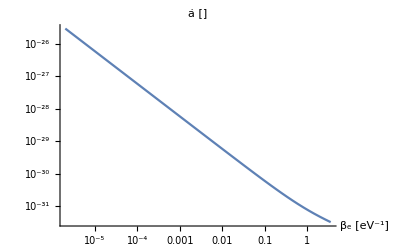

```mathematica
LogLogPlot[aH[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

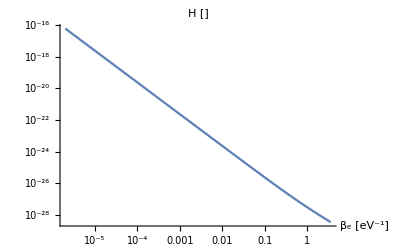

```mathematica
LogLogPlot[H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"H []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

#### Screening length comparison and Expected rate scaling

Λ and 1/(Z_1 β ȧ) control the scaling of the rate

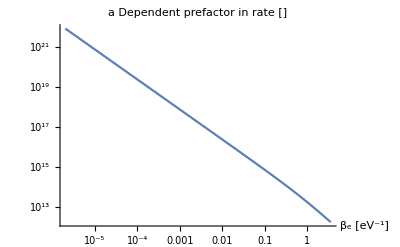

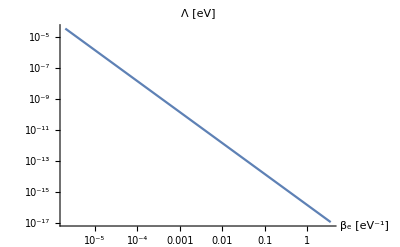

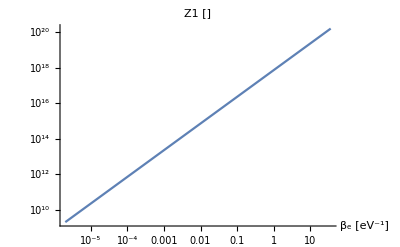

```mathematica
LogLogPlot[1/(Z1[β] aH[β]β)/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"a Dependent prefactor in rate []",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Λ[β,"me"]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Z1[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],10/("TR")/.CosmoParams[]},PlotLabel->"Z1 []",AxesLabel->{"β_e [eV^-1]"}]
```

So it seems like partition function dominates over temperature scaling of a, and the reduced screening at late times.

```mathematica
Z1[1/("Td")]/.CosmoParams[]
```

2.00913×10^9

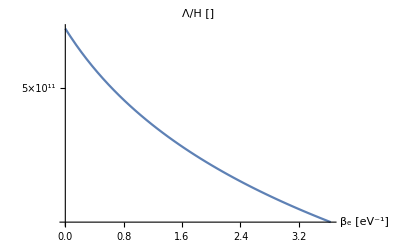

```mathematica
LogPlot[Λ[β,"me"]/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

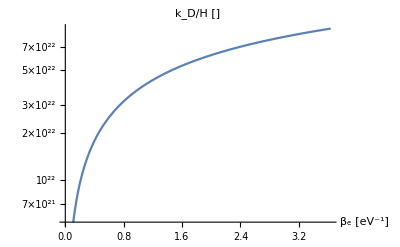

```mathematica
LogPlot[(√(2 "me" Λ[β,"me"]))/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

#### Rate and Energy plots - SM aDM mass values

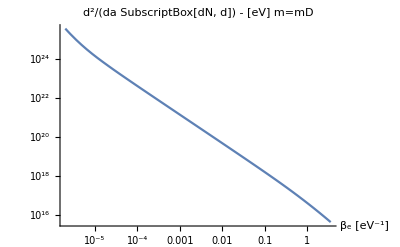

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

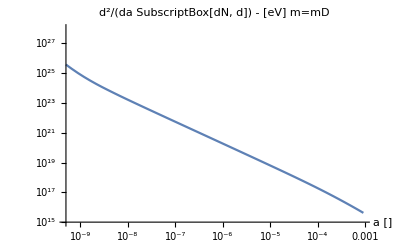

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

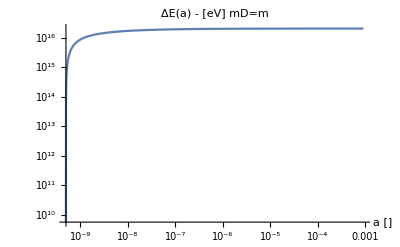

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

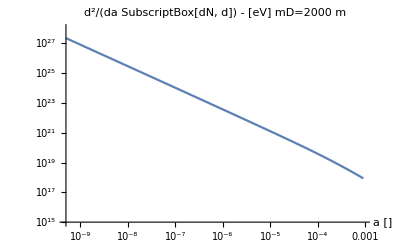

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

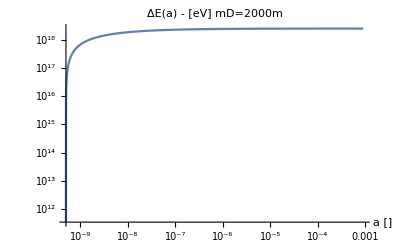

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

#### Neff constraint

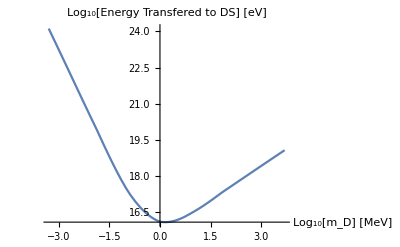

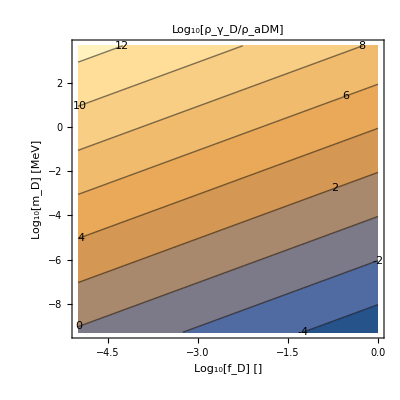

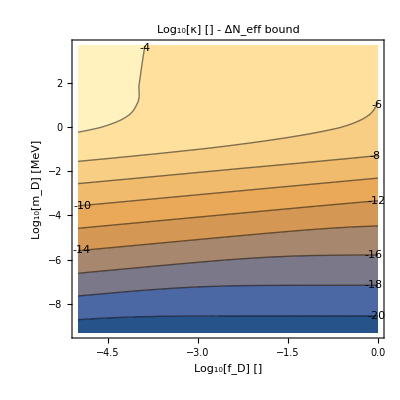

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

#### Interaction Rate - IR domination Debugging

```mathematica
(*ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ,params_]:=(m/.params)/ξβ NIntegrate[ NumIntegrand[mD,m,κ,ξβ,ξE,params],{ξE,0,∞}](*extra factor comes from jacobian*)*)
```

```mathematica
inter1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

```mathematica
interrate1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

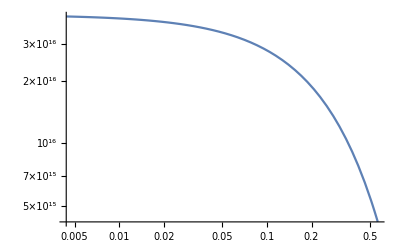

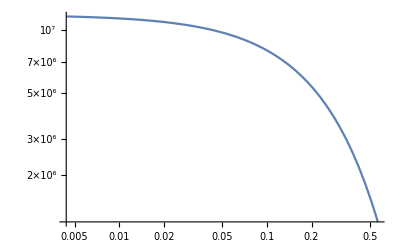

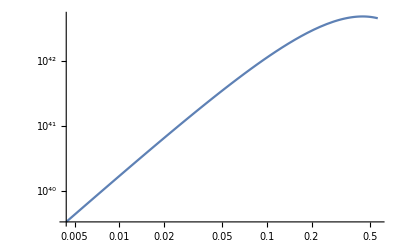

```mathematica
LogLogPlot[10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[nDR[10^-2,interrate1me[["mD"]]]10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[(10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]])/H[β]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
```

```mathematica
nDR[10^-2,10^6]/.CosmoParams[]
```

1.42034×10^-10

```mathematica
Plot[NeffConstraint`ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,ξβ,CosmoParams[],1],{ξβ,1,10^6}]
```

$Aborted

```mathematica
?ESMIntegral
```

```mathematica
NeffConstraint`NumIntegrand["me"/.CosmoParams[],"me"/.CosmoParams[],1,10^5,10^-5,CosmoParams[],0]
```

0.293113

```mathematica
Block[{l=1,Integrand,params=CosmoParams[],v1,v2,v3},
v1=Simplify[Integrate[Ett^l/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett]];
	v2=Simplify[v1/."ms"->("m"^2+"mD"^2)/(2 "mD")];
	v3 =Simplify[Simplify[(v2/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(v2/.Ett->0)]];
Integrand=2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"]^l v3 /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β","me"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params;
(*Print[v1];
Print[v2];*)
(*Print[Integrand];*)
Print[Integrand/.{"m"->"me"/.CosmoParams[],"mD"->"me"/.CosmoParams[],"κ"->1}/.CosmoParams[]]
]
```

(8.95453×10^31 ⅇ^(-((mt+(mt ξE)/ξβ) ξβ)/mt+(ξβ (mt-(mt Log[(7.10335×10^17)/(mt/ξβ)^(3/2)])/ξβ))/mt) mt κ^2 (-((mDt^2+mt^2)^2)/(2 mDt^2)+(2 (mt^2+mDt (mDt-2 (mt+(mt ξE)/ξβ)-(2.91415×10^-16 mt^2)/ξβ^2)) (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(2 mDt^2)/((-1+(mDt+mt+(mt ξE)/ξβ)^2/(-mt^2+(mt+(mt ξE)/ξβ)^2))^2)-2 (mt+(mt ξE)/ξβ)^2-(2.12306×10^-32 mt^4)/ξβ^4+(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(1.45707×10^-16 mt^2 (((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(2.12306×10^-32 mt^4)/ξβ^4-(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2))/(((2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2) ξβ^2)-(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2+(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2]-(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(1.45707×10^-16 mt^2)/ξβ^2]))/(mDt √(0.68+(2.4064×10^10 mt^4)/ξβ^4+(2.048×10^10 mt^3)/ξβ^3+(160000. mt^2)/ξβ^2) ξβ)

```mathematica
-2 ("ESMt"-"ms"+"Λ") Ett+Ett^2/2+("Λ" (2 ("ESMt")^2+2 ("ms")^2+2 "ESMt" "Λ"-2 "ms" "Λ"+("Λ")^2))/("Λ"+Ett)+(2 ("ESMt")^2+2 ("ms")^2+4 "ESMt" "Λ"-4 "ms" "Λ"+3 ("Λ")^2) Log["Λ"+Ett]/."ms"->("m"^2+"mD"^2)/(2 "mD")
Simplify[%]
```

-2 (ESMt-(m^2+mD^2)/(2 mD)+Λ) Ett+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

((m^2+mD (-2 ESMt+mD-2 Λ)) Ett)/mD+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

```mathematica
-1/(DΣ-1)+Simplify[-1/(DΣ-1)+DΣ/(DΣ-1)^2]
Simplify[(1-DΣ/(DΣ-1))^2]
```

1/(-1+DΣ)^2-1/(-1+DΣ)

1/(-1+DΣ)^2

### CMB Distortion

#### Yushin’s BOTE Calculation from CMB distortion

Today

```mathematica
(α^2 ϵ^2 Mpl)/T0^4(eV^3 nD0[0.01,10^9]/.CosmoParams[] ) /.{α->1/137,T0->("T0"/.CosmoParams[]) eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

1.4555×10^16 ϵ^2

8.28884×10^-9

At Recombination

```mathematica
(α^2 ϵ^2 Mpl)/T^4(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

1.32318×10^17 ϵ^2

2.7491×10^-9

```mathematica
(α^2 ϵ^2 Mpl)/T^4 r^-1(eV^3 nD0[0.01,10^9](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV,r->10^-4}
PowerExpand[%]^-1 ϵ^2
```

1.32318×10^17 ϵ^2

7.55754×10^-18

```mathematica
(α^2 ϵ^2 Mpl)/(T^3 me) r^-1(eV^3 nD0[0.01,10^9](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV,r->10^-4,me->"me"eV/.CosmoParams[]}
PowerExpand[%]^-1 ϵ^2
```

7.2775×10^10 ϵ^2

1.3741×10^-11

Yushin was also saying something about DOFs and entropy sharing

100 units of total energy stay in SM sector (some temperature, rad dominated), DS is in TE with SM so entropy split among DS and SM dofs => change of temperature, must be less than 10^{-5}. \Delta N_{eff} is from cosmo bounds etc.
Assumption here seems to be that the sectors equilibriate if they scatter at all.

```mathematica
(α^2 ϵ^2)/T^2(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV,r->10^-5}
```

1.00066×10^-12 eV ϵ^2

#### Squiggly CMB distortion using our interaction rate

get interaction rate (over n_D) for elecron mass aDM scattering off SM electrons with κ=(α_D ϵ)/α = 1

```mathematica
intratemDisme=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0];
```

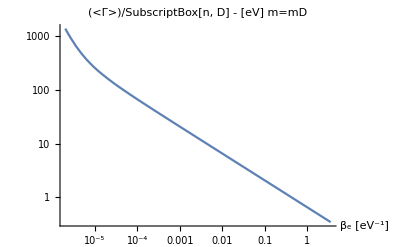

```mathematica
LogLogPlot[10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"(<Γ>)/SubscriptBox[n, D] - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

this shows the interaction rate scales as T^(1/2) near recombination

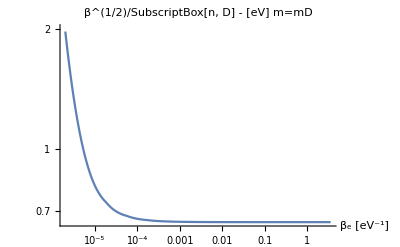

```mathematica
LogLogPlot[β^(1/2)10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(1/2)/SubscriptBox[n, D] - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,2}]
```

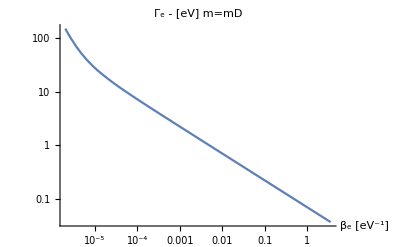

```mathematica
LogLogPlot[(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Γ_e - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

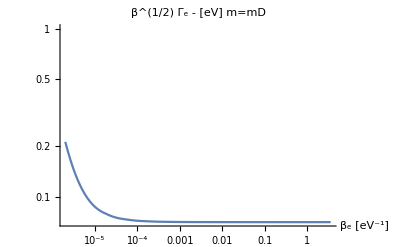

```mathematica
LogLogPlot[β^(1/2)(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(1/2) Γ_e - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,1}]
```

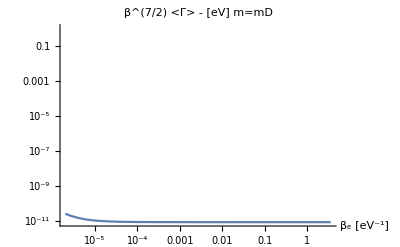

```mathematica
LogLogPlot[β^(7/2)(nD0[0.01,1000"me"/.CosmoParams[]](1/(β "T0"))^3/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(7/2) <Γ> - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,1}]
```

Now compute ((Γ̄)_e)/H

```mathematica
(*H=1/(10^28 eV β^2)*)
ΓebarbyH=1/(H[β]/.CosmoParams[])((nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[]))10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]]/.β->(1/("TR")/.CosmoParams[])
```

1.03254×10^27

```mathematica
ϵ^2== r/ΓebarbyH/.r->10^-5
```

ϵ^2==9.68485×10^-33

This is much too stringent. Now compute (n_e(Γ̄)_e)/H

```mathematica
(*H=1/(10^28 eV β^2)*)
ΓebarbyH=1/(H[β]/.CosmoParams[])(nD0[0.01,1000"me"/.CosmoParams[]](1/(β "T0"))^3/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]]/.β->(1/("TR")/.CosmoParams[])
```

2.71448×10^15

```mathematica
ϵmax = √(r/ΓebarbyH)/.r->10^-4
```

1.91936×10^-10

```mathematica
"n0"(("TR")/("T0"))^3/.CosmoParams[]
```

2.62894×10^-12

```mathematica
("TR")^-3/.CosmoParams[]
```

48.0841

### Scaling Sanity Checks

We want to check that we have the right scalings analytically. 

So we put the initial SM energy on it’s thermal average and take the limit of small temperature compared to mass of SM electron, and with mD = m

This gives the scaling of the interaction rate near recombination.

#### Using expression from the code

```mathematica
Clear[unavdxsection,powereexpanded]
```

```mathematica
unavdxsection=m/ξβ Simplify[NonNumIntegrand[m,m,κ,ξβ,ξE,0]]/.ξE-> β(ESM-m)/.ξβ->β  m/."g"->4 (*g is electron dofs*)
```

(α ⅇ^(-((ESM-m) β)) (1/(Tdt β))^(3/2) κ^2 (Tdt^3 (ESM-m) m β^2 (64 n0^2 α^2 π^4+12 n0 Tdt^3 α (ESM-m) m π^2 β^2+Tdt^6 m^2 β^2 ((ESM-m)^2 β^2+2 (ESM-m) m β^2+2 m^2 β^2))+8 n0 α (8 n0 α π^3+Tdt^3 (ESM-m) m π β^2)^2 Log[(8 n0 α π^2)/(Tdt^3 m β^2)]-8 n0 α (8 n0 α π^3+Tdt^3 (ESM-m) m π β^2)^2 Log[(8 n0 α π^2+Tdt^3 (ESM-m) m β^2)/(Tdt^3 m β^2)]))/(8 pth^3 Tdt^3 m^2 π^3 β^3 (8 n0 α π^2+Tdt^3 (ESM-m) m β^2))

We p (ESM = p^2/(2 m)) on it’s average thermal value. (p_(th,i))^2 =(3 m T)/π so p_th^2 =(9 m T)/π and p_th =3 √2 √((m T)/(2π))

```mathematica
pthav=3 √2 √((2 m)/(β 2 π))
```

3 √(2/π) √(m/β)

```mathematica
Simplify[unavdxsection /. ESM->√(m^2+pthav^2)];
powereexpanded=Simplify[Series[%/. β-> ϵ/m,{ϵ,∞,1}]]
```

SeriesData::slnc: Argument O[1/ϵ]^2 in Log is a series with no coefficients.

General::stop: Further output of SeriesData::slnc will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0 n0 Tdt^6 α π^2 (-∞))/m^2 encountered.

Infinity::indet: Indeterminate expression (0 n0 Tdt^6 α π (-∞))/m encountered.

Infinity::indet: Indeterminate expression (0 n0 Tdt^6 α π^2 (-∞))/m^2 encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

ⅇ^((1-(√(m^2))/m) ϵ-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ϵ)+O[1/ϵ]^2) ((Tdt^4 α (m/(Tdt ϵ))^(5/2) ϵ^(5/2) κ^2 √(1/ϵ))/(4 pth^3 π^3)+O[1/ϵ]^(3/2))

```mathematica
Simplify[PowerExpand[Normal[powereexpanded/."pth"->√((m "Tdt")/(2 π))]/.ϵ->m/T]]
leadingΓ = PowerExpand[Normal[Series[%/.T->ϵ m,{ϵ,0,1}]]/.ϵ->T/m]
```

(α ⅇ^((9 (-2 π+(9 T)/m))/(2 π^2)) √m √T κ^2)/(√2 π^(3/2))

(α ⅇ^(-9/π) √m √T κ^2)/(√2 π^(3/2))

This is dimensionless!!! there is absolutely a bug in this code. It should have dimension 4 or 1. 

I think the reason we are down by a factor of  α is because the Λ factor contains α, so I imagine the leading term in the expansion goes like (Λ)^-1

*****Ah no this is inconsistent with our above scalings. And it’s because there is a factor of m/ξβ from the jacobian.

```mathematica
N[leadingΓ eV/. m->"me"/.T->"TR"/.CosmoParams[]]
```

0.0195898 eV κ^2

Compare this to BOE calculation by Yushin

```mathematica
(α^2 ϵ^2)/T^2(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV}
```

1.00066×10^-12 eV ϵ^2

So there' s a discrepency of 10^10 which looks like it mainly comes from the nD0 factor

```mathematica
nD0[0.01,10^5]("T0" eV)^-3/.CosmoParams[]
```

(6.82957×10^-8)/eV^3

#### Rederiving expression by coding it very clearly and explicitly - with E^2 + Λ^2 propagator

Because these are so wildly different, I think it is worth recoding the numerical integral to ensure there’s no bug in there. This will be good either way since the current implementation is difficult to parse

```mathematica
PΜ=("ms"+ESM)^2+("ms"+(Et-ESM))^2;
prefactor = ("n0")/("T0" β)^3 1/("Z1")((4 π"α")^2 κ^2)/(mD (2 π)^3) ("g")/4 ;(* prefactor of eqn (629) of notes over nD*)
integrand=E^(-β(ESM-m))PΜ/(Et^2 + ("Λ")^2)Et^l;
boundsE= {m,∞};
boundsEt={0,(2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1) };
shorthandrepl={"ms"->(m^2+mD^2)/(2 mD),"Λ"->4π "α" (2 π "n0")/(m "T0") (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};
Integrate[integrand/. l->0,Et]
Etintegral=((%/.Et->boundsEt[[2]])-(%/.Et->boundsEt[[1]]))
```

ⅇ^((-ESM+m) β) (Et+((2 ms^2-Λ^2+2 ESM^2) ArcTan[Et/Λ])/Λ+(ms-ESM) Log[Λ^2+Et^2])

-ⅇ^((-ESM+m) β) (ms-ESM) Log[Λ^2]+ⅇ^((-ESM+m) β) ((2 mD)/(-1+(ESM+mD)^2/(ESM^2-m^2))+((2 ms^2-Λ^2+2 ESM^2) ArcTan[(2 mD)/(Λ (-1+(ESM+mD)^2/(ESM^2-m^2)))])/Λ+(ms-ESM) Log[Λ^2+(4 mD^2)/((-1+(ESM+mD)^2/(ESM^2-m^2))^2)])

```mathematica
pthav=3 √2 √((2 m)/(β 2 π))
 m/ξβ Etintegral/.shorthandrepl/.ESM->√(pthav^2+m^2)/.β->ξβ/m/.mD->m
powereexpanded=Series[%,{ξβ,∞,0}]
```

3 √(2/π) √(m/β)

1/ξβ m (-ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) (m-√(m^2+(18 m^2)/(π ξβ))) Log[(64 n0^2 α^2 m^2 π^4)/(T0^6 ξβ^4)]+ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) ((2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))+(T0^3 (2 m^2+2 (m^2+(18 m^2)/(π ξβ))-(64 n0^2 α^2 m^2 π^4)/(T0^6 ξβ^4)) ξβ^2 ArcTan[(T0^3 ξβ^2)/(4 n0 α π^2 (-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2)))])/(8 n0 α m π^2)+(m-√(m^2+(18 m^2)/(π ξβ))) Log[(64 n0^2 α^2 m^2 π^4)/(T0^6 ξβ^4)+(4 m^2)/((-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))^2)]))

SeriesData::slnc: Argument O[1/ξβ]^4 in Log is a series with no coefficients.

SeriesData::slnc: Argument O[1/ξβ]^2 in Log is a series with no coefficients.

General::stop: Further output of SeriesData::slnc will be suppressed during this calculation.

ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) Log[O[1/ξβ]^4] O[1/ξβ]^1+ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) (((m+√(m^2))^2 √((T0^6 m^4 ξβ^2)/(n0^2 α^2 (m+√(m^2))^4)) ξβ)/(4 π ξβ)-((m+√(m^2))^2 (4 π^3 ξβ-81 √((T0^6 m^4 ξβ^2)/(n0^2 α^2 (m+√(m^2))^4))))/(36 (π^2 ξβ))+O[1/ξβ]^1)

```mathematica
PowerExpand[powereexpanded]
leadingEtterm=(("T0")^3 ⅇ^(-9/π) m^2 ξβ)/(4 "n0" "α" π)
```

Log[O[1/ξβ]^4] O[1/ξβ]^1+((T0^3 ⅇ^(-9/π) m^2 ξβ)/(4 n0 α π)+(ⅇ^(-9/π) m^2 ((729 T0^3)/4+(81 T0^3 π)/2-8 n0 α π^4))/(18 n0 α π^3)+O[1/ξβ]^1)

(T0^3 ⅇ^(-9/π) m^2 ξβ)/(4 n0 α π)

```mathematica
PowerExpand[Simplify[prefactor leadingEtterm /. shorthandrepl]/.ξβ->β m]
%/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[]
%nD0[0.01,2000 "me"]/("n0")/.CosmoParams[]
```

(α ⅇ^(-9/π) m^(3/2) κ^2)/(2 mD √(2 π) √β)

0.0307715 κ^2

0.00166249 κ^2

```mathematica
nD0[0.01,2000 "me"]/("n0")/.CosmoParams[]
```

0.054027

```mathematica
Λrepl={"Λ0"->4π "α" (2 π "n0")/(m "T0")}
```

{Λ0→(8 n0 α π^2)/(T0 m)}

```mathematica
shorthandreplkeepΛ={"ms"->(m^2+mD^2)/(2 mD),"Λ"->"Λ0" (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};
pthav=3 √2 √((2 m)/(β 2 π))
 m/ξβ Etintegral/.shorthandreplkeepΛ/.ESM->√(pthav^2+m^2)/.β->ξβ/m/.mD->m
powereexpanded=Series[%,{ξβ,∞,0}]
```

3 √(2/π) √(m/β)

1/ξβ m (-ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) (m-√(m^2+(18 m^2)/(π ξβ))) Log[(Λ0^2 m^4)/(T0^4 ξβ^4)]+ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) ((2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))+(T0^2 (2 m^2+2 (m^2+(18 m^2)/(π ξβ))-(Λ0^2 m^4)/(T0^4 ξβ^4)) ξβ^2 ArcTan[(2 T0^2 ξβ^2)/(Λ0 m (-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2)))])/(Λ0 m^2)+(m-√(m^2+(18 m^2)/(π ξβ))) Log[(Λ0^2 m^4)/(T0^4 ξβ^4)+(4 m^2)/((-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))^2)]))

SeriesData::slnc: Argument O[1/ξβ]^4 in Log is a series with no coefficients.

SeriesData::slnc: Argument O[1/ξβ]^2 in Log is a series with no coefficients.

General::stop: Further output of SeriesData::slnc will be suppressed during this calculation.

ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) Log[O[1/ξβ]^4] O[1/ξβ]^1+ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) ((2 (m+√(m^2))^2 π √((T0^4 m^2 ξβ^2)/(Λ0^2 (m+√(m^2))^4)) ξβ)/ξβ-((m+√(m^2))^2 (π ξβ-162 √((T0^4 m^2 ξβ^2)/(Λ0^2 (m+√(m^2))^4))))/(9 ξβ)+O[1/ξβ]^1)

```mathematica
PowerExpand[powereexpanded]
leadingEtterm=(2 ("T0")^2 ⅇ^(-9/π) m π ξβ)/("Λ0")
```

Log[O[1/ξβ]^4] O[1/ξβ]^1+((2 T0^2 ⅇ^(-9/π) m π ξβ)/Λ0-(4 (ⅇ^(-9/π) m^2 (-(729 T0^2)/(4 m)-(81 T0^2 π)/(2 m)+Λ0 π^2)))/(9 (Λ0 π))+O[1/ξβ]^1)

(2 T0^2 ⅇ^(-9/π) m π ξβ)/Λ0

```mathematica
PowerExpand[Simplify[prefactor leadingEtterm /. shorthandrepl]/.ξβ->β m]
%/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[]
%nD0[0.01,2000 "me"]/("n0")/.CosmoParams[]
```

(2 √2 n0 α^2 ⅇ^(-9/π) √m π^(3/2) κ^2)/(T0 Λ0 mD √β)

(2.80227×10^-25 κ^2)/Λ0

(1.51398×10^-26 κ^2)/Λ0

```mathematica
"Λ0"/.Λrepl
%/.CosmoParams[]
```

(8 n0 α π^2)/(T0 m)

(4.55335×10^-18)/m

#### Rederiving expression by coding it very clearly and explicitly - with (E + Λ)^2 propagator

Realized after changing over to E^2 + Λ^2 that I had it right in the first place (the code is correct)

```mathematica
PΜ=("ms"+ESM)^2+("ms"+(Et-ESM))^2;
prefactor = ("n0")/("T0" β)^3 1/("Z1")((4 π"α")^2 κ^2)/(mD (2 π)^3) ("g")/4 ;(* prefactor of eqn (629) of notes over nD*)
integrand=E^(-β(ESM-m))PΜ/(Et + "Λ")^2 Et^l
boundsE= {m,∞};
boundsEt={0,(2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1) };
(*shorthandrepl={"ms"->(m^2+mD^2)/(2 mD),"Λ"->4π "α" (2 π "n0")/(m "T0") (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};*)
thermalrepl={"Λ"->"Λ0" (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};
Λrepl={"Λ0"->4π "α" (2 π "n0")/(m "T0")}
msrepl = {"ms"->(m^2+mD^2)/(2 mD)}
pthav=3 √2 √((2 m)/(β 2 π)) (*average thermal momentum for boltzman distributed species (ie for SM electrons)*)
Integrate[integrand/. l->0,Et]
Etintegral=((%/.Et->boundsEt[[2]])-(%/.Et->boundsEt[[1]]))
```

(ⅇ^(-((ESM-m) β)) Et^l ((ms+ESM)^2+(ms-ESM+Et)^2))/(Λ+Et)^2

{Λ0→(8 n0 α π^2)/(T0 m)}

{ms→(m^2+mD^2)/(2 mD)}

3 √(2/π) √(m/β)

ⅇ^((-ESM+m) β) (Et+(-2 ms^2+2 ms Λ-Λ^2-2 Λ ESM-2 ESM^2)/(Λ+Et)-2 (-ms+Λ+ESM) Log[Λ+Et])

-ⅇ^((-ESM+m) β) ((-2 ms^2+2 ms Λ-Λ^2-2 Λ ESM-2 ESM^2)/Λ-2 (-ms+Λ+ESM) Log[Λ])+ⅇ^((-ESM+m) β) ((2 mD)/(-1+(ESM+mD)^2/(ESM^2-m^2))+(-2 ms^2+2 ms Λ-Λ^2-2 Λ ESM-2 ESM^2)/(Λ+(2 mD)/(-1+(ESM+mD)^2/(ESM^2-m^2)))-2 (-ms+Λ+ESM) Log[Λ+(2 mD)/(-1+(ESM+mD)^2/(ESM^2-m^2))])

```mathematica
m/ξβ Etintegral/.thermalrepl/.ESM->√(pthav^2+m^2)/.β->ξβ/m/.mD->m
powereexpanded=Series[%,{ξβ,∞,0}]
```

1/ξβ m (-ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) ((T0^2 (-2 ms^2-2 (m^2+(18 m^2)/(π ξβ))-(Λ0^2 m^4)/(T0^4 ξβ^4)+(2 ms Λ0 m^2)/(T0^2 ξβ^2)-(2 Λ0 m^2 √(m^2+(18 m^2)/(π ξβ)))/(T0^2 ξβ^2)) ξβ^2)/(Λ0 m^2)-2 (-ms+√(m^2+(18 m^2)/(π ξβ))+(Λ0 m^2)/(T0^2 ξβ^2)) Log[(Λ0 m^2)/(T0^2 ξβ^2)])+ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) ((2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))+(-2 ms^2-2 (m^2+(18 m^2)/(π ξβ))-(Λ0^2 m^4)/(T0^4 ξβ^4)+(2 ms Λ0 m^2)/(T0^2 ξβ^2)-(2 Λ0 m^2 √(m^2+(18 m^2)/(π ξβ)))/(T0^2 ξβ^2))/((Λ0 m^2)/(T0^2 ξβ^2)+(2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2)))-2 (-ms+√(m^2+(18 m^2)/(π ξβ))+(Λ0 m^2)/(T0^2 ξβ^2)) Log[(Λ0 m^2)/(T0^2 ξβ^2)+(2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))]))

ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) (-((ms^2+m^2) (m+√(m^2))^2 π)/(18 m^2)+O[1/ξβ]^1)+ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) ((2 T0^2 (ms^2+m^2) ξβ)/(Λ0 m)+(36 T0^2 m)/(Λ0 π)+O[1/ξβ]^1)

```mathematica
PowerExpand[powereexpanded]
leadingEtterm=(2 ("T0")^2 ⅇ^(-9/π) (("ms")^2+m^2) ξβ)/("Λ0" m)
```

(2 T0^2 ⅇ^(-9/π) (ms^2+m^2) ξβ)/(Λ0 m)+((81 T0^2 ⅇ^(-9/π) (ms^2+m^2))/(Λ0 m π^2)+(36 T0^2 ⅇ^(-9/π) m)/(Λ0 π)-2/9 ⅇ^(-9/π) (ms^2+m^2) π)+O[1/ξβ]^1

(2 T0^2 ⅇ^(-9/π) (ms^2+m^2) ξβ)/(Λ0 m)

```mathematica
Print["Leading interaction rate (in T/m_e<< 1), per SM electron, with dark electrons \nevaluated at average thermal momentum of SM electrons is: "]
leadingEttermsubbed=("nD0")/("n0")PowerExpand[Simplify[prefactor leadingEtterm /.thermalrepl]/.ξβ->β m]/.msrepl//Simplify
Print["Same expression assuming m_D=m=m_e"]
%%/.mD->m/.m->"me"
Print["Λ_0 is debeye screening energy (times T_0^2/T^2), and is given by: "]
"Λ0"==("Λ0"/.Λrepl)
leadingEttermsubbed/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[];
% /."nD0"->nD0[0.01,2000 "me"]/.CosmoParams[];
Print["This gives a numerical value for the interaction rate:"]
%%/.Λrepl/.m->"me"/.CosmoParams[]
```

Leading interaction rate (in T/m_e<< 1), per SM electron, with dark electrons 
evaluated at average thermal momentum of SM electrons is:

(nD0 α^2 ⅇ^(-9/π) (m^4+6 m^2 mD^2+mD^4) √(π/2) κ^2)/(T0 Λ0 m^(3/2) mD^3 √β)

Same expression assuming m_D=m=m_e

(4 nD0 α^2 ⅇ^(-9/π) √(2 π) κ^2)/(√me T0 Λ0 √β)

Λ_0 is debeye screening energy (times T_0^2/T^2), and is given by:

Λ0==(8 n0 α π^2)/(T0 m)

This gives a numerical value for the interaction rate:

0.00105838 κ^2

```mathematica
leadingEttermsubbed/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[]
% /."nD0"->nD0[0.01,2000 "me"]/.CosmoParams[]
%/.Λrepl/.m->"me"/.CosmoParams[]
```

(0.0000903209 nD0 κ^2)/Λ0

(9.63832×10^-27 κ^2)/Λ0

0.00105838 κ^2

```mathematica
"Λ0"/.Λrepl/.m->"me"/.CosmoParams[]
```

9.10671×10^-24

```mathematica
thermalrepl
```

{Λ→Λ0/(T0^2 β^2),Z1→g/(2 √2 π^(3/2) (β/m)^(3/2))}

```mathematica
?H
```

```mathematica
H["TR"]/.CosmoParams[]
```

3.45255×10^-27

#### Rederiving expression by coding it very clearly and explicitly - with (E + Λ)^2 propagator on Et average thermal momentum

Realized after changing over to E^2 + Λ^2 that I had it right in the first place (the code is correct)

```mathematica
PΜ=("ms"+ESM)^2+("ms"+(Et-ESM))^2;
prefactor = ("n0")/("T0" β)^3 1/("Z1")((4 π"α")^2 κ^2)/(mD (2 π)^3) ("g")/4 ;(* prefactor of eqn (629) of notes over nD*)
integrand=E^(-β(ESM-m))PΜ/(Et + "Λ")^2 Et^l
boundsE= {m,∞};
boundsEt={0,(2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1) };
(*shorthandrepl={"ms"->(m^2+mD^2)/(2 mD),"Λ"->4π "α" (2 π "n0")/(m "T0") (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};*)
thermalrepl={"Λ"->"Λ0" (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};
Λrepl={"Λ0"->4π "α" (2 π "n0")/(m "T0")}
msrepl = {"ms"->(m^2+mD^2)/(2 mD)}
pthav=3 √2 √((2 m)/(β 2 π)) (*average thermal momentum for boltzman distributed species (ie for SM electrons)*)
Integrate[integrand/. l->0,Et];
(*Etintegral=((%/.Et->boundsEt[[2]])-(%/.Et->boundsEt[[1]]))*)
Etintegral= Et  integrand/.l->0/.Et->pthav^2/(2 m)
```

(ⅇ^(-((ESM-m) β)) Et^l ((ms+ESM)^2+(ms-ESM+Et)^2))/(Λ+Et)^2

{Λ0→(8 n0 α π^2)/(T0 m)}

{ms→(m^2+mD^2)/(2 mD)}

3 √(2/π) √(m/β)

(9 ⅇ^(-((ESM-m) β)) ((ms+ESM)^2+(ms-ESM+9/(π β))^2))/(π (Λ+9/(π β))^2 β)

```mathematica
m/ξβ Etintegral/.thermalrepl/.ESM->√(pthav^2+m^2)/.β->ξβ/m/.mD->m
powereexpanded=Series[%,{ξβ,∞,0}]
```

(9 ⅇ^(-((-m+√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) m^2 ((ms+√(m^2+(18 m^2)/(π ξβ)))^2+(ms-√(m^2+(18 m^2)/(π ξβ))+(9 m)/(π ξβ))^2))/(π ((Λ0 m^2)/(T0^2 ξβ^2)+(9 m)/(π ξβ))^2 ξβ^2)

ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)+O[1/ξβ]^2) (2/9 (ms^2+m^2) π+O[1/ξβ]^1)

```mathematica
PowerExpand[powereexpanded]
(*leadingEtterm=(2 ⅇ^(-9/π) (("ms")^2+m^2) π^2 ξβ)/(81 m)*)
leadingEtterm = 2/9 ⅇ^(-9/π) (("ms")^2+m^2) π
```

2/9 ⅇ^(-9/π) (ms^2+m^2) π+O[1/ξβ]^1

2/9 ⅇ^(-9/π) (ms^2+m^2) π

```mathematica
Print["Leading interaction rate (in T/m_e<< 1), per SM electron, with dark electrons \nevaluated at average thermal momentum of SM electrons is: "]
leadingEttermsubbed=("nD0")/("n0")PowerExpand[Simplify[prefactor leadingEtterm /.thermalrepl]/.ξβ->β m]/.msrepl//Simplify
Print["Same expression assuming m_D=m=m_e"]
%%/.mD->m/.m->"me"
Print["Λ_0 is debeye screening energy (times T_0^2/T^2), and is given by: "]
"Λ0"==("Λ0"/.Λrepl)
leadingEttermsubbed/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[];
% /."nD0"->nD0[0.01,2000 "me"]/.CosmoParams[];
Print["This gives a numerical value for the interaction rate:"]
Γsquiggle=%%/.Λrepl/.m->"me"/.CosmoParams[]
Print["This gives an ϵ bound (√(10^-5/Γ)) of:"]
ϵ<=(10^-4(H[1/("TR")]/.CosmoParams[]))/Γsquiggle κ^2
```

Leading interaction rate (in T/m_e<< 1), per SM electron, with dark electrons 
evaluated at average thermal momentum of SM electrons is:

(nD0 α^2 ⅇ^(-9/π) (m^4+6 m^2 mD^2+mD^4) π^(3/2) κ^2)/(9 √2 T0^3 m^(3/2) mD^3 β^(3/2))

Same expression assuming m_D=m=m_e

(4 √2 nD0 α^2 ⅇ^(-9/π) π^(3/2) κ^2)/(9 √me T0^3 β^(3/2))

Λ_0 is debeye screening energy (times T_0^2/T^2), and is given by:

Λ0==(8 n0 α π^2)/(T0 m)

This gives a numerical value for the interaction rate:

1.48034×10^-20 κ^2

This gives an ϵ bound (√(10^-5/Γ)) of:

ϵ≤2.42976×10^-13

```mathematica
ϵ==(10^-4(H[1/("TR")]/.CosmoParams[]))/Γsquiggle κ^2
```

ϵ==2.42976×10^-13

#### Use the above analysis for energy computation - with (E + Λ)^2 propagator

Realized after changing over to E^2 + Λ^2 that I had it right in the first place (the code is correct)

```mathematica
PΜ=("ms"+ESM)^2+("ms"+(Et-ESM))^2;
prefactor = ("n0")/("T0" β)^3 1/("Z1")((4 π"α")^2 κ^2)/(mD (2 π)^3) ("g")/4 ;(* prefactor of eqn (629) of notes over nD*)
integrand=E^(-β(ESM-m))PΜ/(Et + "Λ")^2 Et^l
boundsE= {m,∞};
boundsEt={0,(2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1) };
(*shorthandrepl={"ms"->(m^2+mD^2)/(2 mD),"Λ"->4π "α" (2 π "n0")/(m "T0") (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};*)
thermalrepl={"Λ"->"Λ0" (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};
Λrepl={"Λ0"->4π "α" (2 π "n0")/(m "T0")}
msrepl = {"ms"->(m^2+mD^2)/(2 mD)}
pthav=3 √2 √((2 m)/(β 2 π)) (*average thermal momentum for boltzman distributed species (ie for SM electrons)*)
Integrate[integrand/. l->1,Et]
EnergyEtintegral=((%/.Et->boundsEt[[2]])-(%/.Et->boundsEt[[1]]))
```

(ⅇ^(-((ESM-m) β)) Et^l ((ms+ESM)^2+(ms-ESM+Et)^2))/(Λ+Et)^2

{Λ0→(8 n0 α π^2)/(T0 m)}

{ms→(m^2+mD^2)/(2 mD)}

3 √(2/π) √(m/β)

ⅇ^((-ESM+m) β) (-2 (-ms+Λ+ESM) Et+Et^2/2+(Λ (2 ms^2-2 ms Λ+Λ^2+2 Λ ESM+2 ESM^2))/(Λ+Et)+(2 ms^2-4 ms Λ+3 Λ^2+4 Λ ESM+2 ESM^2) Log[Λ+Et])

-ⅇ^((-ESM+m) β) (2 ms^2-2 ms Λ+Λ^2+2 Λ ESM+2 ESM^2+(2 ms^2-4 ms Λ+3 Λ^2+4 Λ ESM+2 ESM^2) Log[Λ])+ⅇ^((-ESM+m) β) ((2 mD^2)/((-1+(ESM+mD)^2/(ESM^2-m^2))^2)-(4 (-ms+Λ+ESM) mD)/(-1+(ESM+mD)^2/(ESM^2-m^2))+(Λ (2 ms^2-2 ms Λ+Λ^2+2 Λ ESM+2 ESM^2))/(Λ+(2 mD)/(-1+(ESM+mD)^2/(ESM^2-m^2)))+(2 ms^2-4 ms Λ+3 Λ^2+4 Λ ESM+2 ESM^2) Log[Λ+(2 mD)/(-1+(ESM+mD)^2/(ESM^2-m^2))])

```mathematica
m/ξβ EnergyEtintegral/.thermalrepl/.ESM->√(pthav^2+m^2)/.β->ξβ/m/.mD->m
powereexpanded=Series[%,{ξβ,∞,2}]
```

1/ξβ m (-ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) (2 ms^2+2 (m^2+(18 m^2)/(π ξβ))+(Λ0^2 m^4)/(T0^4 ξβ^4)-(2 ms Λ0 m^2)/(T0^2 ξβ^2)+(2 Λ0 m^2 √(m^2+(18 m^2)/(π ξβ)))/(T0^2 ξβ^2)+(2 ms^2+2 (m^2+(18 m^2)/(π ξβ))+(3 Λ0^2 m^4)/(T0^4 ξβ^4)-(4 ms Λ0 m^2)/(T0^2 ξβ^2)+(4 Λ0 m^2 √(m^2+(18 m^2)/(π ξβ)))/(T0^2 ξβ^2)) Log[(Λ0 m^2)/(T0^2 ξβ^2)])+ⅇ^(((m-√(m^2+(18 m^2)/(π ξβ))) ξβ)/m) ((2 m^2)/((-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))^2)-(4 m (-ms+√(m^2+(18 m^2)/(π ξβ))+(Λ0 m^2)/(T0^2 ξβ^2)))/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))+(Λ0 m^2 (2 ms^2+2 (m^2+(18 m^2)/(π ξβ))+(Λ0^2 m^4)/(T0^4 ξβ^4)-(2 ms Λ0 m^2)/(T0^2 ξβ^2)+(2 Λ0 m^2 √(m^2+(18 m^2)/(π ξβ)))/(T0^2 ξβ^2)))/(T0^2 ξβ^2 ((Λ0 m^2)/(T0^2 ξβ^2)+(2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))))+(2 ms^2+2 (m^2+(18 m^2)/(π ξβ))+(3 Λ0^2 m^4)/(T0^4 ξβ^4)-(4 ms Λ0 m^2)/(T0^2 ξβ^2)+(4 Λ0 m^2 √(m^2+(18 m^2)/(π ξβ)))/(T0^2 ξβ^2)) Log[(Λ0 m^2)/(T0^2 ξβ^2)+(2 m)/(-1+(π (m+√(m^2+(18 m^2)/(π ξβ)))^2 ξβ)/(18 m^2))]))

ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)-(729 √(m^2))/(2 (m π^3) ξβ^2)+O[1/ξβ]^3) (-(2 (m (ms^2+m^2+ms^2 Log[(Λ0 m^2)/(T0^2 ξβ^2)]+m^2 Log[(Λ0 m^2)/(T0^2 ξβ^2)])))/ξβ-(36 (m^3 (1+Log[(Λ0 m^2)/(T0^2 ξβ^2)])))/(π ξβ^2)+O[1/ξβ]^3)+ⅇ^(((m-√(m^2)) ξβ)/m-(9 √(m^2))/(m π)+(81 √(m^2))/(2 m π^2 ξβ)-(729 √(m^2))/(2 (m π^3) ξβ^2)+O[1/ξβ]^3) ((2 m (ms^2+m^2) Log[(36 m^3)/((m+√(m^2))^2 π ξβ)])/ξβ+1/(9 T0^2 (m+√(m^2))^2 π ξβ^2)4 m^2 (162 ms T0^2 m^2-81 ms^2 T0^2 √(m^2)-243 T0^2 (m^2)^(3/2)+2 ms^2 Λ0 m^2 π^2+2 Λ0 m^4 π^2+2 ms^2 Λ0 m √(m^2) π^2+2 Λ0 m^3 √(m^2) π^2+162 T0^2 m^3 Log[(36 m^3)/((m+√(m^2))^2 π ξβ)]+162 T0^2 (m^2)^(3/2) Log[(36 m^3)/((m+√(m^2))^2 π ξβ)])+O[1/ξβ]^3)

```mathematica
PowerExpand[Normal[powereexpanded]]
```

ⅇ^(-9/π-729/(2 π^3 ξβ^2)+81/(2 π^2 ξβ)) (-(2 m (ms^2+m^2+ms^2 (-2 Log[T0]+Log[Λ0]+2 Log[m]-2 Log[ξβ])+m^2 (-2 Log[T0]+Log[Λ0]+2 Log[m]-2 Log[ξβ])))/ξβ-(36 m^3 (1-2 Log[T0]+Log[Λ0]+2 Log[m]-2 Log[ξβ]))/(π ξβ^2))+ⅇ^(-9/π-729/(2 π^3 ξβ^2)+81/(2 π^2 ξβ)) (1/(9 T0^2 π ξβ^2)(-81 ms^2 T0^2 m+162 ms T0^2 m^2-243 T0^2 m^3+4 ms^2 Λ0 m^2 π^2+4 Λ0 m^4 π^2+324 T0^2 m^3 (2 Log[2]+2 Log[3]+3 Log[m]-2 (Log[2]+Log[m])-Log[π]-Log[ξβ]))+(2 m (ms^2+m^2) (2 Log[2]+2 Log[3]+3 Log[m]-2 (Log[2]+Log[m])-Log[π]-Log[ξβ]))/ξβ)

```mathematica
PowerExpand[powereexpanded]
SimpedExpression=FullSimplify[Normal[%]]
leadingEtterm=(2 ⅇ^(-9/π) m (("ms")^2+m^2) (-1+2 Log[3]+2 Log["T0"]-Log["Λ0"]-Log[m]-Log[π]+Log[ξβ]))/ξβ
```

(2 ⅇ^(-9/π) m (ms^2+m^2) (-1+2 Log[3]+2 Log[T0]-Log[Λ0]-Log[m]-Log[π]+Log[ξβ]))/ξβ+1/(9 T0^2 π^2 ξβ^2)ⅇ^(-9/π) (-729 ms^2 T0^2 m-729 T0^2 m^3-81 ms^2 T0^2 m π+162 ms T0^2 m^2 π-567 T0^2 m^3 π+4 ms^2 Λ0 m^2 π^3+4 Λ0 m^4 π^3+1458 ms^2 T0^2 m Log[3]+1458 T0^2 m^3 Log[3]+648 T0^2 m^3 π Log[3]+1458 ms^2 T0^2 m Log[T0]+1458 T0^2 m^3 Log[T0]+648 T0^2 m^3 π Log[T0]-729 ms^2 T0^2 m Log[Λ0]-729 T0^2 m^3 Log[Λ0]-324 T0^2 m^3 π Log[Λ0]-729 ms^2 T0^2 m Log[m]-729 T0^2 m^3 Log[m]-324 T0^2 m^3 π Log[m]-729 ms^2 T0^2 m Log[π]-729 T0^2 m^3 Log[π]-324 T0^2 m^3 π Log[π]+729 ms^2 T0^2 m Log[ξβ]+729 T0^2 m^3 Log[ξβ]+324 T0^2 m^3 π Log[ξβ])+O[1/ξβ]^3

1/(9 T0^2 π^2 ξβ^2)ⅇ^(-9/π) m (-729 ms^2 T0^2-729 T0^2 m^2-81 ms^2 T0^2 π+162 ms T0^2 m π-567 T0^2 m^2 π+4 ms^2 Λ0 m π^3+4 Λ0 m^3 π^3-18 T0^2 (ms^2+m^2) π^2 ξβ+36 T0^2 (ms^2+m^2) π^2 ξβ Log[T0]+162 T0^2 (9 ms^2+m^2 (9+4 π)) Log[3 T0]+9 T0^2 (-((ms^2 (81+2 π^2 ξβ)+m^2 (81+2 π (18+π ξβ))) Log[Λ0])-2 (ms^2+m^2) π^2 ξβ Log[m]-9 (9 ms^2+m^2 (9+4 π)) (Log[m]+Log[π]-Log[ξβ])+2 (ms^2+m^2) π^2 ξβ Log[(9 ξβ)/π]))

(2 ⅇ^(-9/π) m (ms^2+m^2) (-1+2 Log[3]+2 Log[T0]-Log[Λ0]-Log[m]-Log[π]+Log[ξβ]))/ξβ

```mathematica
FullSimplify[Normal[leadingEtterm]/.ξβ->β m]
```

(2 ⅇ^(-9/π) (ms^2+m^2) (-1+2 Log[T0]-Log[m]-Log[Λ0 π]+Log[9 m β]))/β

(2 T0^2 ⅇ^(-9/π) (ms^2+m^2) ξβ)/(Λ0 m)

```mathematica
Print["Leading interaction rate (in T/m_e<< 1), per SM electron, with dark electrons \nevaluated at average thermal momentum of SM electrons is: "]
leadingEttermsubbed=("nD0")/("n0")PowerExpand[Simplify[prefactor leadingEtterm /.thermalrepl]/.ξβ->β m]/.msrepl//Simplify
Print["Same expression assuming m_D=m=m_e"]
%%/.mD->m/.m->"me"
Print["Λ_0 is debeye screening energy (times T_0^2/T^2), and is given by: "]
"Λ0"==("Λ0"/.Λrepl)
leadingEttermsubbed/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[];
% /."nD0"->nD0[0.01,2000 "me"]/.CosmoParams[];
Print["This gives a numerical value for the interaction rate:"]
%%/.Λrepl/.m->"me"/.CosmoParams[]
```

Leading interaction rate (in T/m_e<< 1), per SM electron, with dark electrons 
evaluated at average thermal momentum of SM electrons is:

(nD0 α^2 ⅇ^(-9/π) (m^4+6 m^2 mD^2+mD^4) √(π/2) κ^2 (-1+2 Log[T0]-Log[Λ0]+Log[(9 β)/π]))/(T0^3 m^(3/2) mD^3 β^(5/2))

Same expression assuming m_D=m=m_e

(4 nD0 α^2 ⅇ^(-9/π) √(2 π) κ^2 (-1+2 Log[T0]-Log[Λ0]+Log[(9 β)/π]))/(√me T0^3 β^(5/2))

Λ_0 is debeye screening energy (times T_0^2/T^2), and is given by:

Λ0==(8 n0 α π^2)/(T0 m)

This gives a numerical value for the interaction rate:

4.40935×10^-19 κ^2

```mathematica
leadingEttermsubbed/.mD->m/.m->"me"/.β->1/("TR")/.CosmoParams[]
% /."nD0"->nD0[0.01,2000 "me"]/.CosmoParams[]
%/.Λrepl/.m->"me"/.CosmoParams[]
```

(0.0000903209 nD0 κ^2)/Λ0

(9.63832×10^-27 κ^2)/Λ0

0.00105838 κ^2

```mathematica
"Λ0"/.Λrepl/.m->"me"/.CosmoParams[]
```

9.10671×10^-24

```mathematica
thermalrepl
```

{Λ→Λ0/(T0^2 β^2),Z1→g/(2 √2 π^(3/2) (β/m)^(3/2))}

```mathematica
?H
```

```mathematica
H[("TR")^-1]/.CosmoParams[]
```

3.59687×10^-29